### Settings

```mathematica
d=3;
a=8;
delta = 1;
rMax=20; 
Z =0.125; 
coord = {{0,0},{d,0}, {-d, 0}, {2*d, 0}, {-2*d, 0} };
```

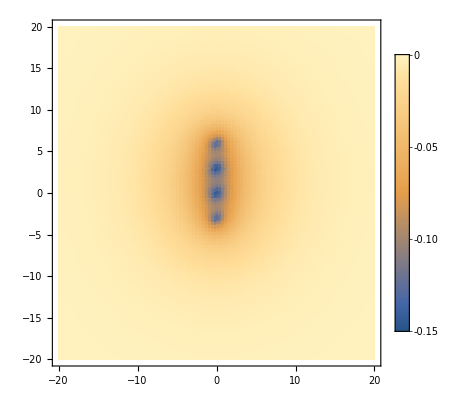

```mathematica
V[r_, θ_] := Sum[(-Z)/(Sqrt[(r*Sin[θ]- coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]+delta)*Exp[-Sqrt[(r*Sin[θ]-coord[[i]][[1]])^2  + (r*Cos[θ]-coord[[i]][[2]])^2]/a],{i,4} ] (*+2*)  ;
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];*)
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
(*DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],*)
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{-0.00299825,-0.00147692,0.00257985,0.00366551,0.00367337,0.00608453,0.00949003,0.00949475}

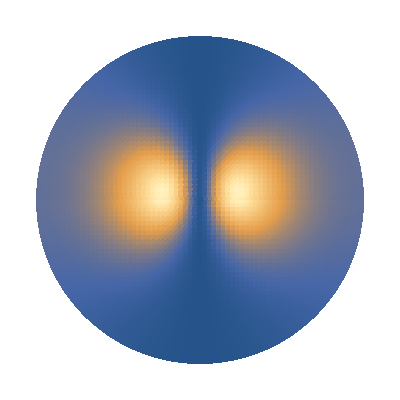

```mathematica
F1 =Part[Re[egnVec],Part[ord,1]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All  (*PlotLegends->Automatic*)];
Show[{%,%%}]
(*Export[NotebookDirectory[]<>"6.png",%,ImageResolution->100];*)
```